```mathematica
(*Mathematica*)
```

```mathematica
(*https://en.wikipedia.org/wiki/PSL(2,7)*)
```

```mathematica
(* graph models od D_7 type polyhedrons:two edge groups 7 fold rotations:91 and 21*)
```

```mathematica
ϵ=(-1+I*Sqrt[7])/2
```

1/2 (-1+ⅈ √7)

```mathematica
ebar=Conjugate[ϵ]
```

1/2 (-1-ⅈ √7)

```mathematica
(* Character table as Killing vectors*)
```

```mathematica
s[1]={1,1,1,1,1,1}
```

{1,1,1,1,1,1}

```mathematica
s[2]={3,-1,1,0,ϵ,ebar}
```

{3,-1,1,0,1/2 (-1+ⅈ √7),1/2 (-1-ⅈ √7)}

```mathematica
s[3]={3,-1,1,0,ebar,ϵ}
```

{3,-1,1,0,1/2 (-1-ⅈ √7),1/2 (-1+ⅈ √7)}

```mathematica
s[4]={6,2,0,0,-1,-1}
```

{6,2,0,0,-1,-1}

```mathematica
s[5]={7,-1,-1,1,0,0}
```

{7,-1,-1,1,0,0}

```mathematica
s[6]={8,0,0,-1,1,1}
```

{8,0,0,-1,1,1}

```mathematica
va=Rationalize[N[Table[s[i].s[i],{i,6}]]]
```

{6,8,8,42,52,67}

```mathematica
(*Casimir invariant*)
```

```mathematica
ci=Rationalize[N[Sum[s[i].s[i],{i,6}]]//Chop]
```

183

```mathematica
(* State probability*)
```

```mathematica
pi=va/ci//Chop
```

{2/61,8/183,8/183,14/61,52/183,67/183}

```mathematica
Apply[Plus,pi]
```

1

```mathematica
(* Character table matrix*)
```

```mathematica
v=Table[s[i],{i,6}]
```

{{1,1,1,1,1,1},{3,-1,1,0,1/2 (-1+ⅈ √7),1/2 (-1-ⅈ √7)},{3,-1,1,0,1/2 (-1-ⅈ √7),1/2 (-1+ⅈ √7)},{6,2,0,0,-1,-1},{7,-1,-1,1,0,0},{8,0,0,-1,1,1}}

```mathematica
ka=N[v.Transpose[v]]//Chop
```

{{6.,2.,2.,6.,6.,9.},{2.,8.,15.,17.,21.,23.},{2.,15.,8.,17.,21.,23.},{6.,17.,17.,42.,40.,46.},{6.,21.,21.,40.,52.,55.},{9.,23.,23.,46.,55.,67.}}

```mathematica
kb=N[Transpose[v].v]//Chop
```

{{168.,0,0,0,0,0},{0,8.,0,0,0,0},{0,0,4.,0,0,0},{0,0,0,3.,0,0},{0,0,0,0,0,7.},{0,0,0,0,7.,0}}

```mathematica
(* Cartan -Graham matrix from Killing vectors*)
```

```mathematica
ca=N[Table[2*s[i].s[j]/(s[i].s[i]),{i,6},{j,6}]]//Chop
```

{{2.,0.666667,0.666667,2.,2.,3.},{0.5,2.,3.75,4.25,5.25,5.75},{0.5,3.75,2.,4.25,5.25,5.75},{0.285714,0.809524,0.809524,2.,1.90476,2.19048},{0.230769,0.807692,0.807692,1.53846,2.,2.11538},{0.268657,0.686567,0.686567,1.37313,1.64179,2.}}

```mathematica
Det[ca]//Chop
Tr[ca]
```

-0.900115

12.

```mathematica
TableForm[ca]
```

2. | 0.666667 | 0.666667 | 2. | 2. | 3.
0.5 | 2. | 3.75 | 4.25 | 5.25 | 5.75
0.5 | 3.75 | 2. | 4.25 | 5.25 | 5.75
0.285714 | 0.809524 | 0.809524 | 2. | 1.90476 | 2.19048
0.230769 | 0.807692 | 0.807692 | 1.53846 | 2. | 2.11538
0.268657 | 0.686567 | 0.686567 | 1.37313 | 1.64179 | 2.

```mathematica
(*characteristic polynomial*)
```

```mathematica
p[x_]=CharacteristicPolynomial[ca,x]//Chop
```

-0.900115+11.8412 x-40.2357 x^2+33.9191 x^3+10.7634 x^4-12. x^5+x^6

```mathematica
rts=x/.NSolve[p[x]==0,x]
```

{-1.75,0.119466,0.302277,0.701089,1.89256,10.7346}

```mathematica
(* relative energy levels from the Eigenvalues*)
```

```mathematica
eg=Eigenvalues[ca]
```

{10.7346,1.89256,-1.75,0.701089,0.302277,0.119466}

```mathematica
Ceiling[{3.7911243385071765,2.297764550381713,1.5555555555555554,1.5555555555555554,0.7999999999999994}]
```

{4,3,2,2,1}

```mathematica
Apply[Plus,eg]/Length[eg]
```

2.

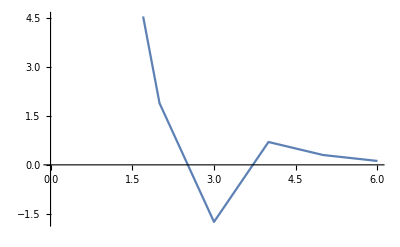

```mathematica
ListLinePlot[eg]
```

```mathematica
WeightedAdjacencyGraph[ca]
```

-Graphics-

```mathematica
aj=Table[If[ca[[i,j]]>0,1,0],{i,6},{j,6}]
```

{{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1}}

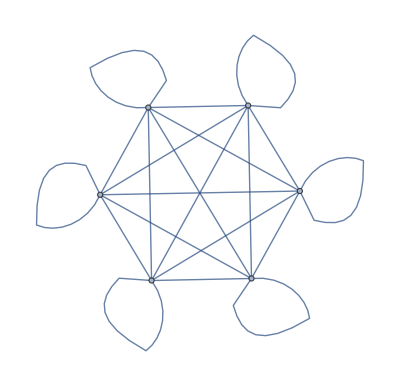

```mathematica
gr=AdjacencyGraph[aj]
```

```mathematica
GraphPlot3D[gr]
```

-Graphics3D-

```mathematica
E0=Table[(-1)^i*pi[[i]]*rts[[i]]*(-1)^j*pi[[j]]/(pi[[i]]*pi[[j]]),{i,6},{j,6}]
```

{{-1.75,1.75,-1.75,1.75,-1.75,1.75},{-0.119466,0.119466,-0.119466,0.119466,-0.119466,0.119466},{0.302277,-0.302277,0.302277,-0.302277,0.302277,-0.302277},{-0.701089,0.701089,-0.701089,0.701089,-0.701089,0.701089},{1.89256,-1.89256,1.89256,-1.89256,1.89256,-1.89256},{-10.7346,10.7346,-10.7346,10.7346,-10.7346,10.7346}}

```mathematica
Ea=E0.Transpose[E0]
```

{{18.375,1.2544,-3.17391,7.36144,-19.8719,112.713},{1.2544,0.0856331,-0.216671,0.502539,-1.35659,7.69453},{-3.17391,-0.216671,0.548227,-1.27154,3.43247,-19.4689},{7.36144,0.502539,-1.27154,2.94916,-7.96114,45.1555},{-19.8719,-1.35659,3.43247,-7.96114,21.4908,-121.896},{112.713,7.69453,-19.4689,45.1555,-121.896,691.39}}

```mathematica
Eigenvalues[Ea]//Chop
```

{734.839,0,0,0,0,0}

```mathematica
q[x_]=ExpandAll[CharacteristicPolynomial[Ea,x]/x^4//Chop]
```

-734.839 x+x^2

```mathematica
x/.NSolve[q[x]==0,x][[1]]
```

0.

```mathematica
Sqrt[%]
```

0.

```mathematica
Transpose[E0].E0
```

{{122.473,-122.473,122.473,-122.473,122.473,-122.473},{-122.473,122.473,-122.473,122.473,-122.473,122.473},{122.473,-122.473,122.473,-122.473,122.473,-122.473},{-122.473,122.473,-122.473,122.473,-122.473,122.473},{122.473,-122.473,122.473,-122.473,122.473,-122.473},{-122.473,122.473,-122.473,122.473,-122.473,122.473}}

```mathematica
(*end*)
```

Lookup::invrl: The argument Missing[NotAvailable] is not a valid Association or a list of rules.